```mathematica
Needs["PlotLegends`"]
```

```mathematica
ClearAll[z,a,d0,b0,ex]
```

```mathematica
v=9;
gap[v][5]= gap5v9;
gap[v][10]= gap10v9;
gap[v][20]= gap20v9;
gap[v][30]= gap30v9;
gap[v][40]= gap40v9;
gap[v][50]= gap50v9;
```

0.42

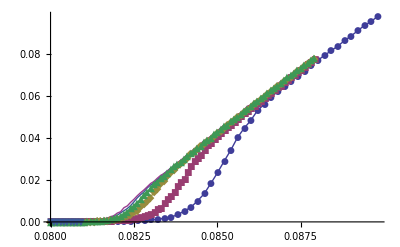

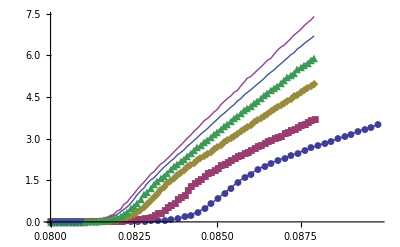

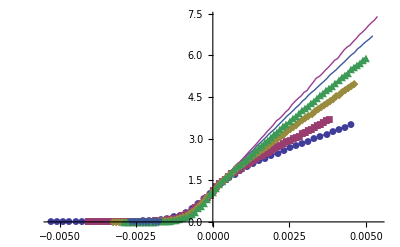

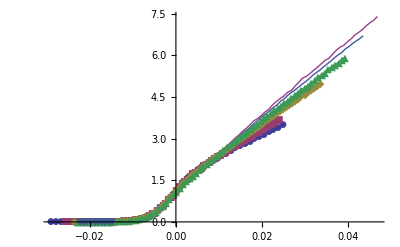

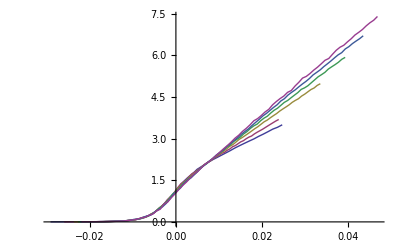

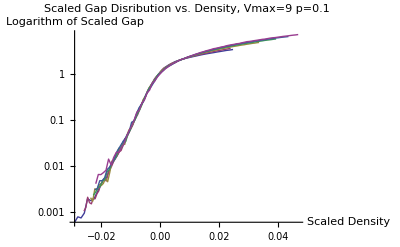

```mathematica
(*a[v]=0.22638171579816446
d0[v]=0.08122007942715888;
b0[v]=0.10133613937361555;
ex[v]=-0.3801025694705213;
z[v]=0.09;*)
a[v]=0.42
d0[v]=0.08122;
b0[v]=0.28130983532217824;
ex[v]=-0.49695262629390596;
z[v]=0.2;
(*a[v]=0.52;
d0[v]=0.08122;
b0[v]=0.37;
ex[v]=-0.515;
z[v]=0.2;*)
Do[
gaps1[v][l]=Table[{gap[v][l][[All,1]][[i]],gap[v][l][[All,2]][[i]]*(1000*l)^a[v]},{i,1,Length[gap[v][l]]}];

gaps2[v][l]=Table[{gap[v][l][[All,1]][[i]]-(d0[v]+b0[v]*(l*1000)^(ex[v])),gap[v][l][[All,2]][[i]]*(1000*l)^a[v]},{i,1,Length[gap[v][l]]}];

gaps[v][l]=Table[{(gap[v][l][[All,1]][[i]]-(d0[v]+b0[v]*(l*1000)^(ex[v])))*(1000*l)^z[v],gap[v][l][[All,2]][[i]]*(1000*l)^a[v]},{i,1,Length[gap[v][l]]}];
,{l,{5,10,20,30,40,50}}]
pic0=ListPlot[{gap[v][5],gap[v][10],gap[v][20],gap[v][30],gap[v][40],gap[v][50]},Joined->True,PlotMarkers->Automatic,PlotRange->Full]
pic1=ListPlot[{gaps1[v][5],gaps1[v][10],gaps1[v][20],gaps1[v][30],gaps1[v][40],gaps1[v][50]},Joined->True,PlotMarkers->Automatic]
pic2=ListPlot[{gaps2[v][5],gaps2[v][10],gaps2[v][20],gaps2[v][30],gaps2[v][40],gaps2[v][50]},Joined->True,PlotMarkers->Automatic]
pic3=ListPlot[{gaps[v][5],gaps[v][10],gaps[v][20],gaps[v][30],gaps[v][40],gaps[v][50]},Joined->True,PlotMarkers->Automatic]
ListLinePlot[{gaps[v][5],gaps[v][10],gaps[v][20],gaps[v][30],gaps[v][40],gaps[v][50]}]
ListLogPlot[{gaps[v][5],gaps[v][10],gaps[v][20],gaps[v][30],gaps[v][40],gaps[v][50]},Joined->True,PlotLabel->"Scaled Gap Disribution vs. Density, Vmax=9 p=0.1",PlotRange->Full,PlotLegend->{"5k","10k","20k","30k","40k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None,AxesLabel->{"Scaled Density","Logarithm of Scaled Gap"},BaseStyle->{FontWeight->"Bold",FontSize->12},RotateLabel->True]
```

```mathematica
PlotLabel->"Scaled Gap Disribution vs. Density, Vmax=9 p=0.1",
```

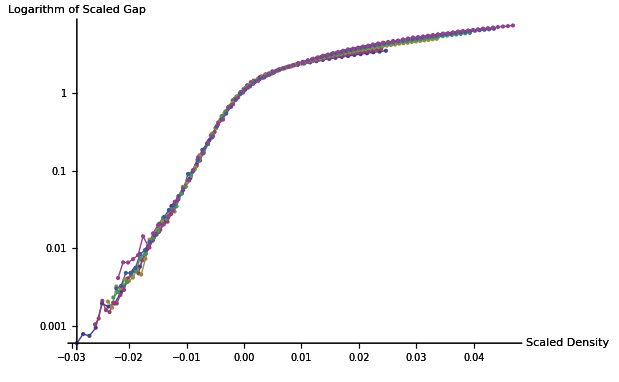

```mathematica
pic11=ListLogPlot[{gaps[v][5],gaps[v][10],gaps[v][20],gaps[v][30],gaps[v][40],gaps[v][50]},Joined->True,PlotRange->Full,PlotLegend->{"5k","10k","20k","30k","40k","50k"},LegendPosition->{0.8,-0.4},LegendShadow->None,AxesLabel->{"Scaled Density","Logarithm of Scaled Gap"},BaseStyle->{FontWeight->"Bold",FontSize->12},RotateLabel->True];
pic22=ListLogPlot[{gaps[v][5],gaps[v][10],gaps[v][20],gaps[v][30],gaps[v][40],gaps[v][50]},PlotRange->Full,PlotLegend->{"5k","10k","20k","30k","40k","50k"},LegendPosition->{0.8,-0.4},LegendShadow->None,AxesLabel->{"Scaled Density","Logarithm of Scaled Gap"},BaseStyle->{FontWeight->"Bold",FontSize->12},RotateLabel->True];
Show[{pic11,pic22}]
```